# Stability of FRW Cosmology with Generalized Chaplygin Gas

-Graphics-

Vamos a considerar el modelo de FRW con el termino de Λ nulo, es decir:
dH/dt=- H^2- 1/6(ρ+3p)=P(H,ρ)
dρ/dt=- 3H(ρ+p)=Q(H,ρ)

que están representadas por el siguiente código:

```mathematica
FieldEq0=H'[t]==-H[t]^2-1/6(ρ[t]+3P[t]);
FieldEq1=ρ'[t]==-3H[t](ρ[t]+P[t]);   (*ecuación de continuidad*)
```

La ecuación de estado por la generalización del gas de Chaplygin de abajo, donde A>0 y 0<α≤1

```mathematica
Eq1=P[t]==-A/ρ[t]^α;
```

### Matriz

Los puntos criticos del espacio de fase, están dados por la matriz linealizada -Graphics-
por lo cual, primero calculamos la matriz

```mathematica
P[H_,ρ_]:=-H^2- 1/6(ρ+3P[ρ]);
Q[H_,ρ_]:=-3H(ρ+P[ρ]);


M={{D[P[H,ρ],H],D[P[H,ρ],ρ]},{D[Q[H,ρ],H],D[Q[H,ρ],ρ]}};	MM=M//MatrixForm
```

(-2 H | 1/6 (-1-3 P'[ρ])
-3 (ρ+P[ρ]) | -3 H (1+P'[ρ]))

El determinante es

```mathematica
Expand[ Det[{{-2 H,1/6 (-1-3 P'[ρ])},{-3 (ρ+P[ρ]),-3 H (1+P'[ρ])}}]]
```

6 H^2-ρ/2-P[ρ]/2+6 H^2 P'[ρ]-3/2 ρ P'[ρ]-3/2 P[ρ] P'[ρ]

Encontramos los puntos criticos

```mathematica
Ec1=-H^2- 1/6(ρ+3P)==0;
Ec2=-3H(ρ+P)==0;

PuntosCriticos=Solve[{Ec1,Ec2},{H,ρ}]
Simplify[PuntosCriticos]
```

{{H→0,ρ→-3 P},{H→-(ⅈ √P)/(√3),ρ→-P},{H→(ⅈ √P)/(√3),ρ→-P}}

{{H→0,ρ→-3 P},{H→-(ⅈ √P)/(√3),ρ→-P},{H→(ⅈ √P)/(√3),ρ→-P}}

Determinamos ρ[t]

```mathematica
ρ'[t]+3H[t](ρ[t]+P[t]);(*=0*)

rules=Solve[{Eq1},P[t]][[1]];
Ec3=dρEq=Expand[D[ρ[t],t]+3H[t](ρ[t]+P[t])/.rules/.H[t]->a'[t]/a[t]]
```

(3 ρ[t] a'[t])/a[t]-(3 A ρ[t]^-α a'[t])/a[t]+ρ'[t]

```mathematica
DSolve[(3 ρ[t] a'[t])/a[t]-(3 A ρ[t]^-α a'[t])/a[t]+ρ'[t]==0,ρ[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ρ[t]→(A-ⅇ^(C[1]+α C[1]) a[t]^(-3-3 α))^(1/(1+α))}}

Y la solución del libro es

Reescribimos la ecuación al del tipo -Graphics-

```mathematica
Ec4=CC==A/Subscript[ρ, 0,chapl]^(1+α); (*Donde CC=Subscript[A, s]*)
Ec5=Subscript[ρ, 0,chapl]==(A+B)^(1/(1+α));
rules1=Solve[{Ec4},A][[1]];

rules2=Solve[{Ec5},B][[1]];
Ec6=Simplify[Expand[ρ[t]-(A+B/a[t]^(3(1+ α)) )^(1/(1+α))==0/.rules1/.rules2/.rules1]] (*Esta es la ecuación 16a*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(a[t]^(-3 (1+α)) (1-CC+CC a[t]^(3+3 α)) ρ_(0,chapl)^(1+α))^(1/(1+α))==ρ[t]

La primera integral de: H'[t]==-H[t]^2-1/6(ρ[t]+3P[t])es ρ[t] = 3 H[t]^2 + (3 k)/a[t]^2, por lo cual reemplazamos ρ[t]

```mathematica
Subscript[Ω, Chapl,0]==Subscript[ρ, 0,chapl]/(3 Subscript[H[t], 0]^2);
a[t]==1/(1+z);
Subscript[Ω, k,0]==-k/Subscript[H[t], 0]^2;
PowerExpand[ρ[t]-(3 k)/a[t]^2==3 H[t]^2/. k->-Subscript[Ω, k,0] Subscript[H[t], 0]^2/.ρ[t]->(a[t]^(-3 (1+α)) (1-CC+CC a[t]^(3+3 α)) Subscript[ρ, 0,chapl]^(1+α))^(1/(1+α))/.Subscript[ρ, 0,chapl]->3 Subscript[H[t], 0]^2 Subscript[Ω, Chapl,0]/.a[t]->1/(1+z)] (*Esta es la ecuación 18 del articulo*)
```

2.1 (1+z)^3 (1-CC+CC (1+z)^(-3-3 α))^(1/(1+α)) H[t]_0^2+3 (1+z)^2 H[t]_0^2 Ω_(k,0)==3 H[t]^2

Se debe de cumplir que Ω_(Chapl,0) + Ω_(k,0)=1

Introducimos la nueva variable temporal τ como una función monotoma del tiempo cosmológico original dτ/dt=1/ρ^α⇒ d/dτ=ρ^α d/dt

```mathematica
(*Definimos el cambio de variable*)
dτ[f_]:=ρ^α D[f[t],t]; (*f es una función cualquiera*)

(*Segunda ecuación de Friedmann*)
friedmann2=H'[t]==-H[t]^2-1/6(ρ[t]+3P[t]);
(*Ecuación de Continuidad*)
Continuidad=ρ'[t]==-3H[t](ρ[t]+P[t]); 

(*Reemplazamos H'[t] con dH/dτ usando la regla de la cadena*)
friedmann2τ=dτ[H]==ρ^α(-H[t]^2-1/6(ρ[t]+3P[t]))/.rules  (*Ecuación 20a*)
(*Reemplazamos ρ'[t] con dρ/dτ usando la regla de la cadena*)
Continuidad2τ=dτ[ρ]==ρ^α(-3H[t](ρ[t]+P[t]))/.rules  (*Ecuación 20b*)
```

ρ^α H'[t]==ρ^α (-H[t]^2+1/6 (-ρ[t]+3 A ρ[t]^-α))

ρ^α ρ'[t]==-3 ρ^α H[t] (ρ[t]-A ρ[t]^-α)

#### IV. FRW MODELS WITH THE CHAPLYGIN GAS AS A HAMILTONIAN SYSTEMS

```mathematica
ρ[t]->(A+Ba[t]^(-3-3 α))^(1/(1+α));
H[t_]:=a'[t]/a[t];
D[H[t],t]//Simplify;

Simplify[PowerExpand[H'[t]==-H[t]^2-1/6(ρ[t]+3P[t])/.P[t]->-A/ρ[t]^α/.ρ[t]->(A+Ba[t]^(-3-3 α))^(1/(1+α))]] (*Esta es la ecuación 23*)
-Graphics-;
```

a''[t]/a[t]==1/6 (2 A-Ba[t]^(-3 (1+α))) (A+Ba[t]^(-3 (1+α)))^(-α/(1+α))

```mathematica
V[a_]:=-1/6(A+B a^(-3-3 α))^(1/(1+α)) a^2+Subscript[V, 0] 
ddota=Simplify[-D[V[a],a]]
```

(a (2 a^(3+3 α) A-B) (A+a^(-3 (1+α)) B)^(1/(1+α)))/(6 (a^(3+3 α) A+B))

```mathematica
firstIntegral=1/2 a'[t]^2+V[a[t]]==Ε
```

-1/6 a[t]^2 (A+B a[t]^(-3-3 α))^(1/(1+α))+V_0+1/2 a'[t]^2==Ε

Si consideramos la función hamiltoniana ℋ=(a')^2/2+V(a). Es útil considerar la dinamica en los niveles de energía igual a cero ℋ=E=0. Entonces tenemos V_0= k/2. Obtenemos el potencial del sistema en la siguiente forma:

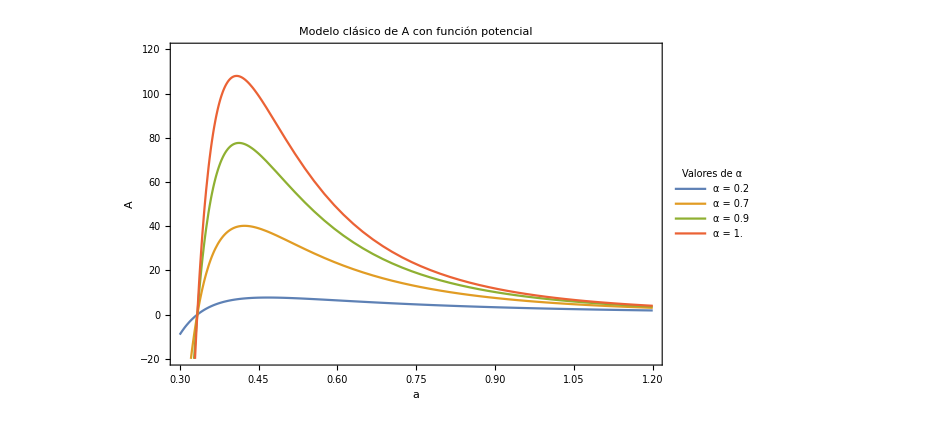

```mathematica
V[a_]:=-1/6(A+B a^(-3-3 α))^(1/(1+α)) a^2+κ/2


(*Definimos la función A con un parametro α*)
A[a_,α_]:=((3 κ)/a^2)^(1+α)-B/a^(3(1+α));
(*Parameter values*)
κ=+1;
αList={0.2,0.7,0.9,1.0};  (*your α values*)
B=1;

(*Grafica para las curvas de α*)
Plot[Evaluate[Table[A[a,α],{α,αList}]],{a,0.3,1.2},PlotStyle->ColorData[97]/@Range[Length[αList]],Frame->True,FrameLabel->{Style["a",Bold,Large],Style["A",Bold,Large]},FrameTicksStyle->Large,PlotLegends->Placed[LineLegend[ColorData[97]/@Range[Length[αList]],(Style["α = "<>ToString[#],16]&/@αList),LegendLabel->Style["Valores de α ",Bold,16]],{0.8,0.5}],PlotRange->{{0.3,1.2},{-20,120}},PlotLabel->"Modelo clásico de A con función potencial",ImageSize->700]
```

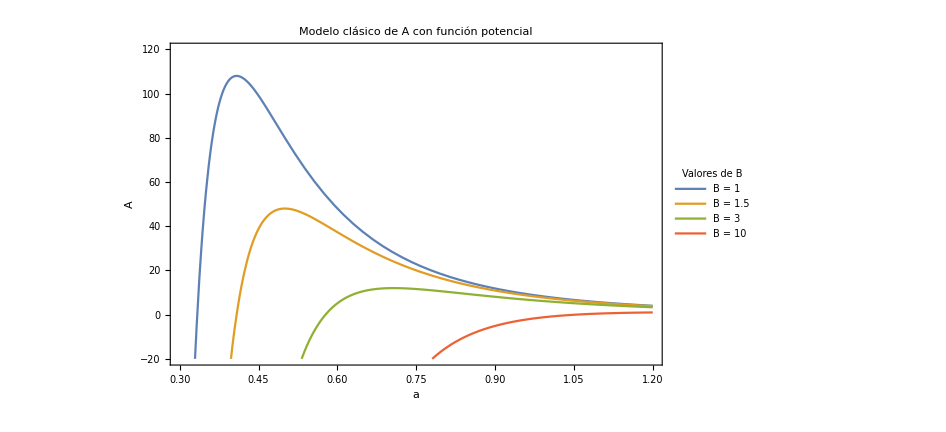

```mathematica
ClearAll["Global`*"]
(*Definimos la función A con un parametro B*)
A[a_,B_]:=((3 κ)/a^2)^(1+α)-B/a^(3(1+α));
(*Parameter values*)
κ=+1;
α=1;  (*your α values*)
BList={1,1.5,3,10};

(*Grafica para las curvas de α*)
Plot[Evaluate[Table[A[a,B],{B,BList}]],{a,0.3,1.2},PlotStyle->ColorData[97]/@Range[Length[BList]],Frame->True,FrameLabel->{Style["a",Bold,Large],Style["A",Bold,Large]},FrameTicksStyle->Large,PlotLegends->Placed[LineLegend[ColorData[97]/@Range[Length[BList]],(Style["B = "<>ToString[#],16]&/@BList),LegendLabel->Style["Valores de B",Bold,16]],{0.8,0.5}],PlotRange->{{0.3,1.2},{-20,120}},PlotLabel->"Modelo clásico de A con función potencial",ImageSize->700]
```

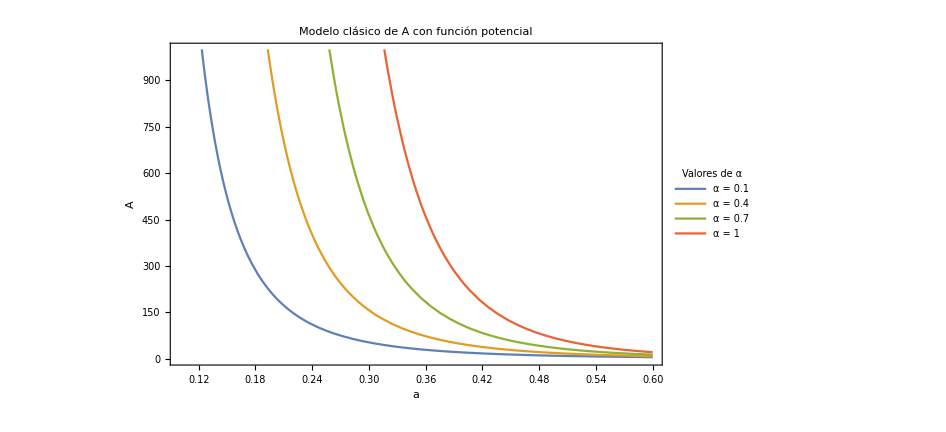

```mathematica
ClearAll["Global`*"]
(*Definimos la función A con un parametro α*)
A[a_,α_]:=((3 κ)/a^2)^(1+α)-B/a^(3(1+α));
(*Parameter values*)
κ=0;
αList={0.1,0.4,0.7,1};  (*your α values*)
B=-1;

(*Grafica para las curvas de α*)
Plot[Evaluate[Table[A[a,α],{α,αList}]],{a,0.1,0.6},PlotStyle->ColorData[97]/@Range[Length[αList]],Frame->True,FrameLabel->{Style["a",Bold,Large],Style["A",Bold,Large]},FrameTicksStyle->Large,PlotLegends->Placed[LineLegend[ColorData[97]/@Range[Length[αList]],(Style["α = "<>ToString[#],16]&/@αList),LegendLabel->Style["Valores de α ",Bold,16]],{0.8,0.5}],PlotRange->{{0.1,0.6},{0,1000}},PlotLabel->"Modelo clásico de A con función potencial",ImageSize->700]
```

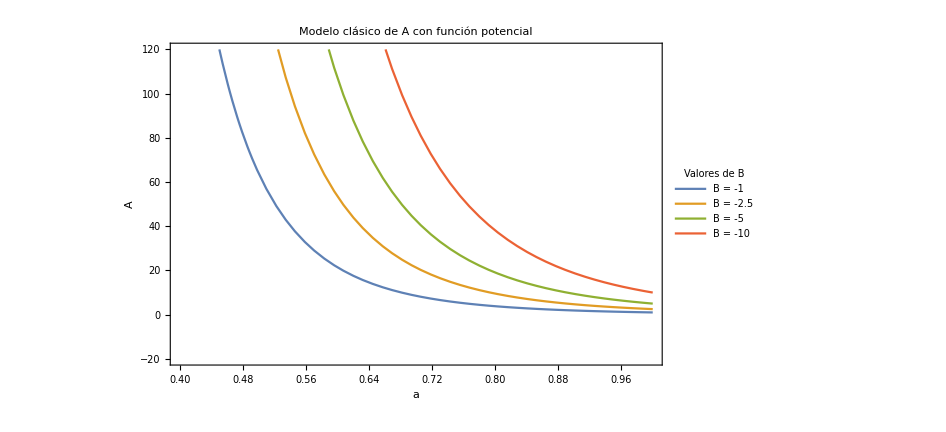

```mathematica
ClearAll["Global`*"]
(*Definimos la función A con un parametro B*)
A[a_,B_]:=((3 κ)/a^2)^(1+α)-B/a^(3(1+α));
(*Parameter values*)
κ=0;
α=1;  (*your α values*)
BList={-1,-2.5,-5,-10};

(*Grafica para las curvas de α*)
Plot[Evaluate[Table[A[a,B],{B,BList}]],{a,0.4,1},PlotStyle->ColorData[97]/@Range[Length[BList]],Frame->True,FrameLabel->{Style["a",Bold,Large],Style["A",Bold,Large]},FrameTicksStyle->Large,PlotLegends->Placed[LineLegend[ColorData[97]/@Range[Length[BList]],(Style["B = "<>ToString[#],16]&/@BList),LegendLabel->Style["Valores de B",Bold,16]],{0.8,0.5}],PlotRange->{{0.4,1},{-20,120}},PlotLabel->"Modelo clásico de A con función potencial",ImageSize->700]
```

Las ecuaciones dinámicas básicas son:

```mathematica
ClearAll["Global`*"]
x[a_]:=a/Subscript[a, 0];
x'[a]^2/2==1/2 Subscript[Ω, k,0]+1/2 Subscript[Ω, Chapl,0](Subscript[A, s]+(1-Subscript[A, s])/x[a]^(3(1+α)))^(1/(1+α))x[a]^2;
V[x_]:=-1/2 Subscript[Ω, k,0]-1/2 Subscript[Ω, Chapl,0](Subscript[A, s]+(1-Subscript[A, s])/x^(3(1+α)))^(1/(1+α))x^2;
xpp=-D[V[x],x] (*Esto es x''=-D[V,x], esta es la ecuación 31*)
```

0.7 x (0.95+0.05 x^(-3 (1+α)))^(1/(1+α))-0.0525 x^(1-3 (1+α)) (0.95+0.05 x^(-3 (1+α)))^(-1+1/(1+α))

### V. LA RELACIÓN DESPLAZAMIENTO AL ROJO-MAGNITUD PARA EL MODELO CON GAS CHAPLYGIN

Una relación del desplazamiento al rojo-magnitud puede utilizarse para determinar el mejor parámetro para el modelo de FRW con un gas de Chaplygin generalizado.
	l: es la luminosidad aparente de la fuente 
	d_L: es la distancia luminosa de la fuente

```mathematica
Subscript[d, L]==(1+z)Subscript[a, 0] Subscript[r, 1];
l=L/(4 π Subscript[d, L]^2);
```

#### La forma integral

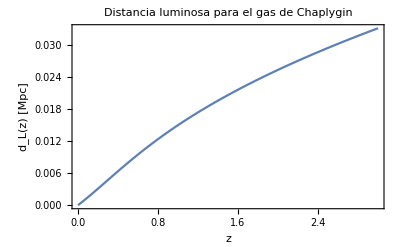

```mathematica
Subscript[Ω, m,0]=0.05;             (*Densidad de materia*)
Subscript[Ω, Chapl,0]=0.95;       (*Densidad del gas de Chaplygin generalizado*)
α=0.51;
Subscript[A, s]=0.73;
Subscript[H, 0]=70; (*Example value in km/s/Mpc*)

dL[z_]:=(1+z)/Subscript[H, 0] NIntegrate[1/(√(Subscript[Ω, m,0](1+r)^3+Subscript[Ω, Chapl,0](Subscript[A, s]+(1-Subscript[A, s])(1+z)^(3(1+α)))^(1/(1+α)))),{r,0,z}];
Plot[dL[z],{z,0,3},Frame->True,FrameLabel->{"z","d_L(z) [Mpc]"},PlotLabel->"Distancia luminosa para el gas de Chaplygin"]
```

#### La forma de una ecuación diferencial

Si lo resolvemos por la ecuación diferencial 

-Graphics-

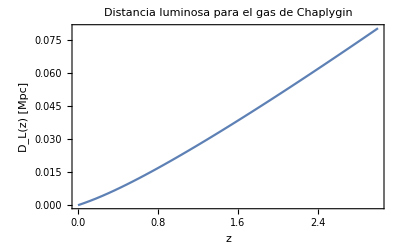

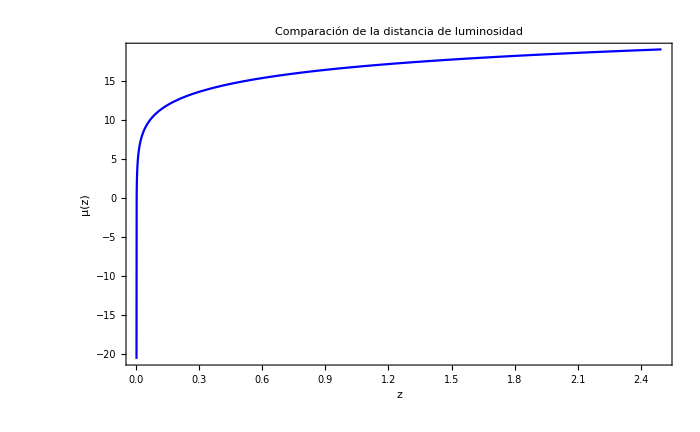

```mathematica
ClearAll["Global`*"]
(*Parametros*)
Subscript[Ω, m,0]=0.05;
Subscript[Ω, Chapl,0]=0.95;
α=0.51;
Subscript[A, s]=0.73;
Subscript[H, 0]=67.11;

(*Función de Hubble H(z)*)
Hz[z_]:=Subscript[H, 0] √(Subscript[Ω, m,0](1+z)^3+Subscript[Ω, Chapl,0](Subscript[A, s]+(1-Subscript[A, s])(1+z)^(3(1+α)))^(1/(1+α)))


(*Solve ODE for D_L(z)*)
solϱModels=NDSolve[{DL'[z]/(1+z)-DL[z]/(1+z)^2-1/Hz[z]==0,DL[0]==0},DL,{z,0,3}];
μDLModels[z_]:=5 Log[10, DL[z]]+25;

(*Plot result*)
Plot[Evaluate[DL[z]/. solϱModels],{z,0,3},Frame->True,FrameLabel->{"z","D_L(z) [Mpc]"},PlotLabel->"Distancia luminosa para el gas de Chaplygin"]

Plot[{Evaluate[μDLModels[z]/. solϱModels]},{z,0,2.5},PlotStyle->{Blue},

Frame->True, FrameLabel->{Style["z", Bold, Large], Style["μ(z)", Bold, Large]}, FrameTicksStyle->Large,
Epilog->Inset[
Framed[
Column[{LineLegend[{Blue}, {Style["μ(z)",20]}, LegendMarkerSize->{10,5}]}], RoundingRadius->2], Scaled[{0.7,0.6}]],PlotRange->All, 
PlotLabel->"Comparación de la distancia de luminosidad",ImageSize->700]
```

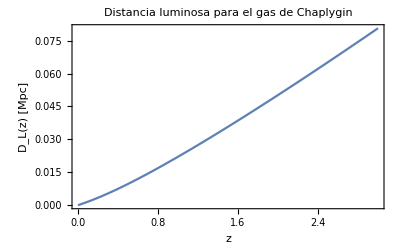

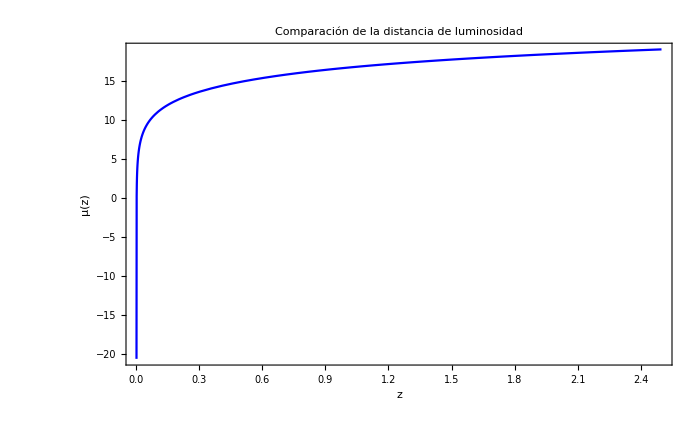

```mathematica
ClearAll["Global`*"]
Subscript[Ω, m,0]=0.3;
Subscript[Ω, Chapl,0]=0.7;
α=0.95;
Subscript[A, s]=0.95;
Subscript[H, 0]=67.11;
(*Hubble function H(z)*)
Hz[z_]:=Subscript[H, 0] √(Subscript[Ω, m,0](1+z)^3+Subscript[Ω, Chapl,0](Subscript[A, s]+(1-Subscript[A, s])(1+z)^(3(1+α)))^(1/(1+α)))

(*Solve ODE for D_L(z)*)
solϱModels=NDSolve[{DL'[z]/(1+z)-DL[z]/(1+z)^2-1/Hz[z]==0,DL[0]==0},DL,{z,0,3}];
μDLModels[z_]:=5 Log[10, DL[z]]+25;

(*Plot result*)
Plot[Evaluate[DL[z]/. solϱModels],{z,0,3},Frame->True,FrameLabel->{"z","D_L(z) [Mpc]"},PlotLabel->"Distancia luminosa para el gas de Chaplygin"]

Plot[{Evaluate[μDLModels[z]/. solϱModels]},{z,0,2.5},PlotStyle->{Blue},

Frame->True, FrameLabel->{Style["z", Bold, Large], Style["μ(z)", Bold, Large]}, FrameTicksStyle->Large,
Epilog->Inset[
Framed[
Column[{LineLegend[{Blue}, {Style["μ(z)",20]}, LegendMarkerSize->{10,5}]}], RoundingRadius->2], Scaled[{0.7,0.6}]],PlotRange->All, 
PlotLabel->"Comparación de la distancia de luminosidad",ImageSize->700]
```

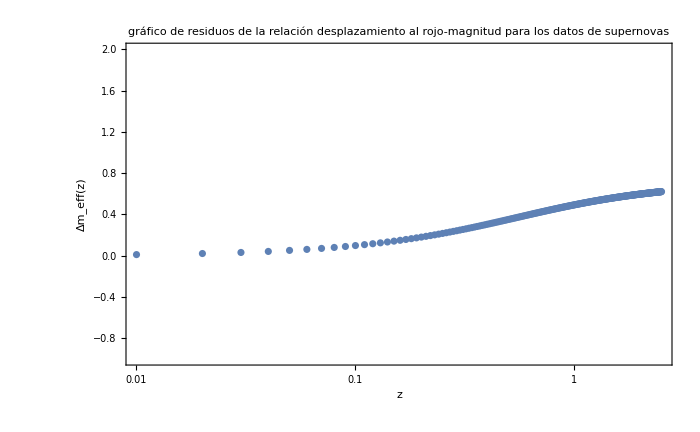

```mathematica
ClearAll["Global`*"]
(*Parameter sets:{Ω_m,Ω_Chapl,α,As}*)
paramsList={{0.05,0.95,0.51,0.73},(*Model 1:Chaplygin gas*)
{0.3,0.7,0.95,0.05}    (*Reference:ΛCDM*)};
H0=67; (*km/s/Mpc*)

(*Function to get H(z) for a given Ω_m,Ω_Chapl,α,As*)
HzFunc[Ωm_,ΩCh_,α_,As_][z_]:=H0 √(Ωm(1+z)^3+ΩCh(As+(1-As)(1+z)^(3(1+α)))^(1/(1+α)));

(*Resolvemos la ED para D_L(z) dados los valores de Ω_m,Ω_Chapl,α,As*)
solveDL[Ωm_,ΩCh_,α_,As_]:=Module[{Hz,sol},Hz=HzFunc[Ωm,ΩCh,α,As];
sol=NDSolve[{DL'[z]/(1+z)-DL[z]/(1+z)^2-1/Hz[z]==0,DL[0]==0},DL,{z,0,2.5}];
First[DL/. sol]  (*Interpolating function*)];

(*Distance modulus function*)
muFromDL[DLif_]:=Function[z,5 Log10[DLif[z]]+25];

(*Solve for both models using parameters from the list*)
DLModel1=solveDL@@paramsList[[1]];
DLRef=solveDL@@paramsList[[2]];

muModel1=muFromDL[DLModel1];
muRef=muFromDL[DLRef];

(*Δm_eff function*)
deltaMeff[z_]:=muModel1[z]-muRef[z];

(*Plot Δm_eff with log-scale on z*)
ListLogLinearPlot[Table[{z,deltaMeff[z]},{z,0.01,2.5,0.01}],Frame->True,FrameLabel->{Style["z",Bold,Large],Style["Δm_eff(z)",Bold,Large]},PlotStyle->Thick,PlotRange->{{0.01,2.5},{-1,2}},GridLines->Automatic,ImageSize->700,PlotLabel->" gráfico de residuos de la relación desplazamiento al rojo-magnitud para los datos de supernovas"]
```

```mathematica
ClearAll["Global`*"]
```

## Data chi χ^2

```mathematica
datosorig={{0.0708,69.0,19.68},{0.09,69.0,12.0},{0.07,69.0,19.68},{0.12,68.6,26.2},{0.17,83.0,8.0},{0.179,75.0,4.0},
{0.199,75.0,5.0},{0.2,72.9,29.6},{0.240,79.69,2.65},
{0.27,77.0,14.0},{0.28,88.8,36.6},{0.35,84.4,7.0},{0.352,83.0,14},{0.4,95,17},{0.43,86.45,3.68},{0.44,82.6,7.8},{0.48,97.0,62.0},{0.57,92.4,4.5},{0.593,104.0,13.0},{0.6,87.9,6.1},{0.68,92.0,8},{0.73,97.3,7},{0.781,105,12},{0.875,125,17},{0.88,90,40},{0.9,117,23},{1.037,154,20},{1.3,168,17},{1.363,160,33.6},{1.43,177,18},{1.53,140,14},{1.75,202,40},{1.965,186.5,50.4},{2.3,224,8},{2.34,222,7},{2.36,226,8},(*{0.510,105.70,1.79},{0.706,115.10,1.26},*){0.934,124.82,1.51},{1.321,149.70,2.33},{1.484,159.06,6.40},{2.330,233.79,2.73},{0.922,115.61,1.39},{0.955,114.70,1.91}};
```

```mathematica
zval=datosorig[[All,1]];
Hval=datosorig[[All,2]];
errors=datosorig[[All,3]];
len=Length[Hval]
data=Table[{zval[[i]],Hval[[i]]},{i,1,len}];
cov=DiagonalMatrix[errors^2];
invcov=Inverse[cov];
```

42

```mathematica
cov//TableForm
```

387.302 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 144. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 387.302 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 686.44 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 64. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 16. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 25. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 876.16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.0225 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 196. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1339.56 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 49. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 196. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 289. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 13.5424 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 60.84 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3844. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 20.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 169. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 37.21 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 64. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 49. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 144. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 289. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1600. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 529. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 400. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 289. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1128.96 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 324. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 196. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1600. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2540.16 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 64. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 49. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 64. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.2801 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.4289 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 40.96 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.4529 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.9321 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.6481

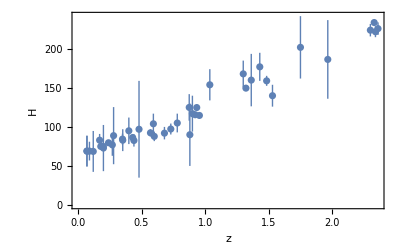

```mathematica
lp=ListPlot[Table[{zval[[i]],Around[Hval[[i]],errors[[i]]]},{i,len}],Frame->True,FrameLabel->{"z","H"}]
```

### Model

```mathematica
NP=2;
H[z_,α_,As_]:=70 √(0.05(1+z)^3+0.95(As+(1-As)(1+z)^(3(1+α)))^(1/(1+α)))
H[z,0.51,0.95]
```

70 √(0.05 (1+z)^3+0.95 (0.95+0.05 (1+z)^4.53)^0.662252)

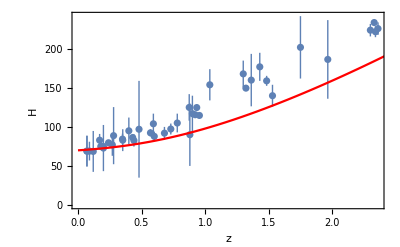

```mathematica
Show[lp,Plot[H[z,0.51,0.95],{z,0,3},PlotStyle->Red]]
```

### Likelihood function with parameters

En este caso haremos que a=α y b=As

```mathematica
amin=0;
amax=1;
astep=0.01;
am=Table[i,{i,amin,amax,astep}]
Length[am]
bmin=0.5;
bmax=0.9;
bstep=0.01;
bm=Table[i,{i,bmin,bmax,bstep}]
Length[bm]
Length[am]*Length[bm]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

101

{0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9}

41

4141

```mathematica
Plot[0,{wa,amin,amax},PlotRange->{{amin,amax},{bmin,bmax}},GridLines->{am,bm},Frame->True,FrameLabel->{"a","b"}]
```

-Graphics-

### build the -2*log-likelihood: (data-theory).InvCov.(data-theory)

Encontramos el mejor ajuste de parametros

```mathematica
count=0;
Do[{
len=Length[Hval];
chi2r[ia,ib]=Sum[((H[zval[[i]],am[[ia]],bm[[ib]]]-Hval[[i]])/errors[[i]])^2,{i,1,len}];
count++;
If[Mod[count,1000]==0 ,Print[count],0]

},{ia,Length[am]},{ib,Length[bm]}]
chi2=Table[chi2r[ia,ib],{ia,Length[am]},{ib,Length[bm]}];
```

1000

2000

3000

4000

```mathematica
minchi=Min[Flatten[chi2]]
```

59.6958

```mathematica
minchi=Min[Flatten[chi2]]
minchi/(len-NP)
lista={};
lista2={};
Do[If[chi2r[ia,ib]==minchi,
mina=am[[ia]];
minb=bm[[ib]];
Print[{mina,minb}];
];
If[chi2r[ia,ib]<200,
lista=Append[lista,{am[[ia]],bm[[ib]],chi2r[ia,ib]}];
lista2=Append[lista2,{am[[ia]],bm[[ib]],Exp[-chi2r[ia,ib]]}]]

,{ia,Length[am]},{ib,Length[bm]}]
lista;
lista2;
```

59.6958

1.49239

{0.,0.75}

El valor 1.49 es el chi-cuadrado reducido, lo cual esta cerca de los valores aceptados [0.7-1.25]

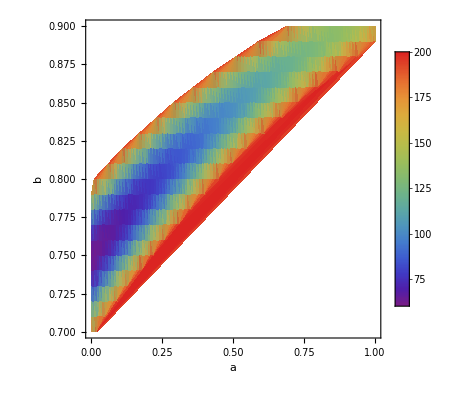

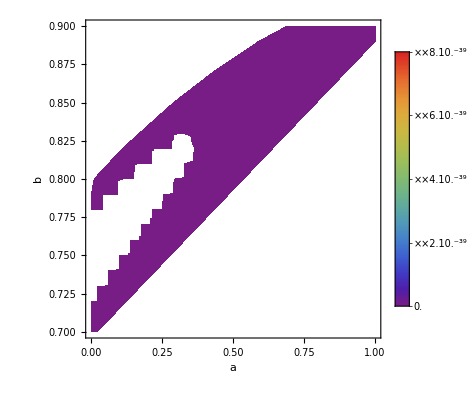

```mathematica
ListDensityPlot[lista, FrameLabel->{"a","b"}, PlotLegends->Automatic, InterpolationOrder->4, ColorFunction->"Rainbow"]
ListDensityPlot[lista2, FrameLabel->{"a","b"}, PlotLegends->Automatic, InterpolationOrder->4, ColorFunction->"Rainbow"]
```

Podemos darnos cuenta de que a=α , b=As podría mejorar en los valores, tal vez tener valores negativos para si poder obtener el mejor ajuste de la figura.

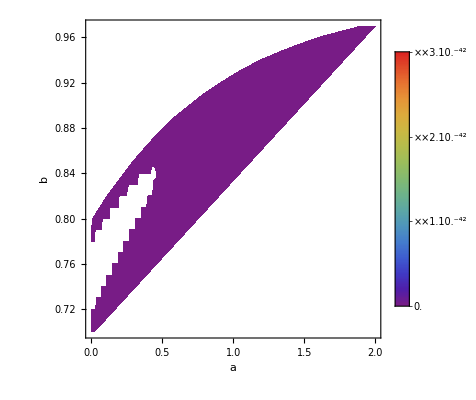

```mathematica
ClearAll["Global`*"]
```

#### Ultima gráfica:

Reducimos el rango de α y As para así poder observar mejor el espacio de fase

```mathematica
(*Datos*)
datosorig={{0.0708,69.0,19.68},{0.09,69.0,12.0},{0.07,69.0,19.68},{0.12,68.6,26.2},{0.17,83.0,8.0},{0.179,75.0,4.0},
{0.199,75.0,5.0},{0.2,72.9,29.6},{0.240,79.69,2.65},
{0.27,77.0,14.0},{0.28,88.8,36.6},{0.35,84.4,7.0},{0.352,83.0,14},{0.4,95,17},{0.43,86.45,3.68},{0.44,82.6,7.8},{0.48,97.0,62.0},{0.57,92.4,4.5},{0.593,104.0,13.0},{0.6,87.9,6.1},{0.68,92.0,8},{0.73,97.3,7},{0.781,105,12},{0.875,125,17},{0.88,90,40},{0.9,117,23},{1.037,154,20},{1.3,168,17},{1.363,160,33.6},{1.43,177,18},{1.53,140,14},{1.75,202,40},{1.965,186.5,50.4},{2.3,224,8},{2.34,222,7},{2.36,226,8},(*{0.510,105.70,1.79},{0.706,115.10,1.26},*){0.934,124.82,1.51},{1.321,149.70,2.33},{1.484,159.06,6.40},{2.330,233.79,2.73},{0.922,115.61,1.39},{0.955,114.70,1.91}};

zval=datosorig[[All,1]];
Hval=datosorig[[All,2]];
errors=datosorig[[All,3]];
len=Length[Hval]
data=Table[{zval[[i]],Hval[[i]]},{i,1,len}];
cov=DiagonalMatrix[errors^2];
invcov=Inverse[cov];
lp=ListPlot[Table[{zval[[i]],Around[Hval[[i]],errors[[i]]]},{i,len}],Frame->True,FrameLabel->{"z","H"}]
(*Modelo*)
NP=2;
H[z_,α_,As_]:=70 √(0.05(1+z)^3+0.95(As+(1-As)(1+z)^(3(1+α)))^(1/(1+α)))
H[z,0.51,0.95];
Show[lp,Plot[H[z,0.51,0.95],{z,0,3},PlotStyle->Red]]

(*Parametros*)
amin=0;
amax=0.11;
astep=0.01;
am=Table[i,{i,amin,amax,astep}];
Length[am];
bmin=0.73;
bmax=0.78;
bstep=0.01;
bm=Table[i,{i,bmin,bmax,bstep}];
Length[bm];
Length[am]*Length[bm];

(*construimos la-2*log-verosimilitud*)

count=0;
Do[{
len=Length[Hval];
chi2r[ia,ib]=Sum[((H[zval[[i]],am[[ia]],bm[[ib]]]-Hval[[i]])/errors[[i]])^2,{i,1,len}];
count++;
If[Mod[count,1000]==0 ,Print[count],0]

},{ia,Length[am]},{ib,Length[bm]}];
chi2=Table[chi2r[ia,ib],{ia,Length[am]},{ib,Length[bm]}];
```

42

-Graphics-

-Graphics-

ListDensityPlot::prng: Value of option PlotRange -> {0,2.29582+minchi} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListDensityPlot::arrayerr: lista must be a valid array.

ListDensityPlot::prng: Value of option PlotRange -> {0,6.18009+minchi} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListDensityPlot::arrayerr: lista must be a valid array.

{0.,0.75}

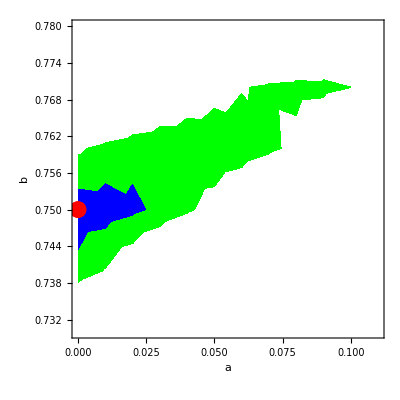

```mathematica
deltachi1=Quantile[ChiSquareDistribution[NP],0.6827];
deltachi2=Quantile[ChiSquareDistribution[NP],0.9545];
cp1=ListDensityPlot[lista,FrameLabel->{"a","b"},InterpolationOrder->4,ColorFunction->(Which[#<=(minchi+deltachi1),Blue]&),ColorFunctionScaling->False,PlotRange->{0,minchi+deltachi1}];
cp2=ListDensityPlot[lista,FrameLabel->{"a","b"},InterpolationOrder->4,ColorFunction->(Which[#<=(minchi+deltachi2),Green]&),ColorFunctionScaling->False,PlotRange->{0,minchi+deltachi2}];

minchi=Min[Flatten[chi2]];
minchi/(len-NP);
lista={};
lista2={};
Do[If[chi2r[ia,ib]==minchi,
mina=am[[ia]];
minb=bm[[ib]];
Print[{mina,minb}];
];
If[chi2r[ia,ib]<200,
lista=Append[lista,{am[[ia]],bm[[ib]],chi2r[ia,ib]}];
lista2=Append[lista2,{am[[ia]],bm[[ib]],Exp[-chi2r[ia,ib]]}]]

,{ia,Length[am]},{ib,Length[bm]}];



deltachi1=Quantile[ChiSquareDistribution[NP],0.6827];
deltachi2=Quantile[ChiSquareDistribution[NP],0.9545];
cp1=ListDensityPlot[lista,FrameLabel->{"a","b"},InterpolationOrder->4,ColorFunction->(Which[#<=(minchi+deltachi1),Blue]&),ColorFunctionScaling->False,PlotRange->{0,minchi+deltachi1}];
cp2=ListDensityPlot[lista,FrameLabel->{"a","b"},InterpolationOrder->4,ColorFunction->(Which[#<=(minchi+deltachi2),Green]&),ColorFunctionScaling->False,PlotRange->{0,minchi+deltachi2}];
Show[cp2,cp1,ListPlot[{{mina,minb}},PlotStyle->{Red,PointSize[0.03]},PlotRange->All]]
```

Estos son el rango de valores para el modelo

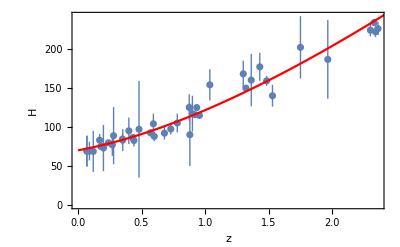

```mathematica
Show[lp,Plot[H[z,mina,minb],{z,0,3},PlotStyle->Red]]
```